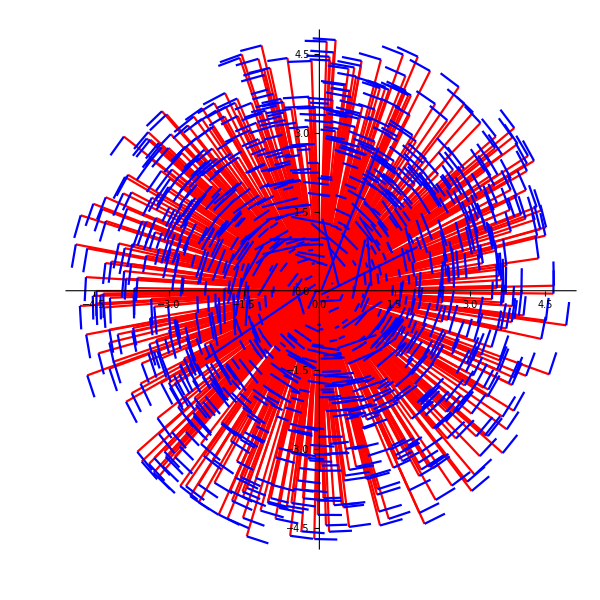

```mathematica
l1=ListPlot[{{0,0},#}&/@clouds⟦All,;;2⟧,Joined->True,PlotStyle->Red];
l2=ListPlot[Table[{clouds⟦i⟧⟦;;2⟧,clouds⟦i⟧⟦;;2⟧+vels⟦i⟧},{i,Length@clouds}],Joined->True,PlotStyle->Blue];
Show[l1,l2,AspectRatio->1]
```

```mathematica
minmass=0.1;
maxmass=10;
α=2.35;
((maxmass^(α+1)-minmass^(α+1))RandomReal[nstars]+minmass^(α+1))^(1/(α+1))
```

17.967

```mathematica
ClearAll["Global`*"]
cart:={r(Cos[ω+ν]Cos[Ω]-Sin[ω+ν]Sin[Ω]Cos[i]),
r(Cos[ω+ν]Sin[Ω]+Sin[ω+ν]Cos[Ω]Cos[i]),
r Sin[ω+ν]Sin[i]+.001};
Ε[M_,e_]=Nest[Kepler,M,10];
Εf=Ε[M,e];
Εff[MM_,ee_]:=N[Εf/.{M->MM,e->ee}];
Kepler[Ε_]:=M+e Sin[Ε];
$Elliptic:={r Cos[ν]:>a(Cos[Ε]-e),r Sin[ν]:>a √(1-e^2)Sin[Ε],t-t0:> 1/n(Ε-e Sin[Ε]),Ε->Kepler[]};
XYZ=Function[{a,e,i,ω,Ω,Ε},TrigExpand[cart]/.$Elliptic//Evaluate];
Geometry[{a_,e_,i_,ω_,Ω_,M_},opts___]:=
{Line[
{{XYZ[a,e,i,ω,Ω,0],XYZ[a,e,i,ω,Ω,180°]}(*a*),
{XYZ[a,e,i,ω,Ω,90°],XYZ[a,e,i,ω,Ω,270°]}(*b*),
{XYZ[a,e,i,ω,Ω,0°],XYZ[a,e,i,ω,Ω,90°]}}]};
```

```mathematica
Εf/.M->1
```

1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1+e Sin[1]]]]]]]]]]

```mathematica
Εff[1,2]
```

1.32403

```mathematica
nd=NotebookDirectory[];
gdata=Import[nd<>"gillessen-2016.txt","Table"];
{as,es,is,ωs,Ωs,Tps,Ps}=gdata⟦Range[1,Length@gdata-5]~Join~Range[Length@gdata-3,Length@gdata],{2,4,6,10,8,12,14}⟧ᵀ;
Ms=(Tps-tnow)/Ps 2π;
Es=Εff[#⟦1⟧,#⟦2⟧]&/@({Ms,es}ᵀ);
coords=XYZ@@#&/@({as,es,is,ωs,Ωs,Es}ᵀ);
coords*=(2π/360/3600)*8000*1191.29;
(*Manipulate[coords⟦1⟧/.tnow->tn,{tn,2010,2030}]*)
Manipulate[ListPointPlot3D[coords/.tnow->tn,PlotRange->50*{{-1,1},{-1,1},{-1,1}},BoxRatios->1],{tn,2010,2030}]
```

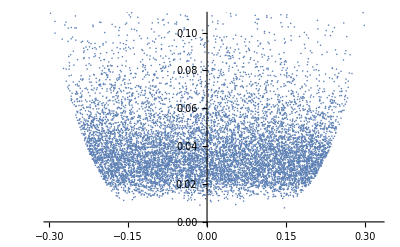

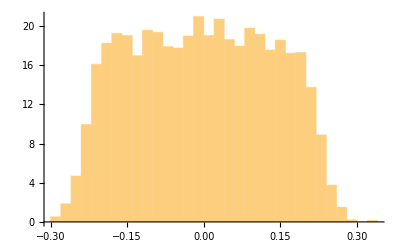

```mathematica
(*ClearAll["Global`*"]
nd=NotebookDirectory[];*)
boxsize=5;
nstars=10;
nclouds=10000;
stars={{0,0,0}}~Join~RandomPoint[Ball[{0,0,0},2*boxsize],nstars];
(*stars=coords;*)
(*stars={{0,0,0}};*)
clouds=4/5 RandomVariate[GammaDistribution[1/0.2^2,1],nclouds]*Normalize/@RandomPoint[Ball[{0,0,0},2*boxsize],nclouds];
vels=1/(Norm/@clouds)^(3/2)(RotationTransform[90°][#⟦;;2⟧]&/@clouds);
losvel={1,0}.#&/@vels;
lums={0.00001}~Join~(10^RandomReal[{-1,1},Length@stars]);
intensities=Total[Table[lums⟦s⟧/Norm[clouds⟦c⟧-stars⟦s⟧]^2,{c,Length@clouds},{s,Length@stars}],{2}];
ListPlot[{losvel,intensities}ᵀ]
vec={losvel,intensities}ᵀ;
vec=Sort[vec,#1⟦1⟧<#2⟦1⟧&];
Histogram[WeightedData[vec⟦All,1⟧,vec⟦All,2⟧]]
(*vec⟦All,2⟧=Accumulate[vec⟦All,2⟧];
vec⟦All,2⟧=Rescale[vec⟦All,2⟧,{0,Max[vec⟦All,2⟧]}];
intf=Interpolation[vec,InterpolationOrder->2];*)
(*line=D[intf[x],x];
Plot[line,{x,Min@losvel,Max@losvel}]*)
```

```mathematica
Manipulate[Show[ListPointPlot3D[clouds,PlotStyle->{Directive[PointSize@0.005,Blue]}],Graphics3D[{Orange,Sphere[#,2]}&/@(coords/.tnow->tn)],PlotRange->50*{{-1,1},{-1,1},{-1,1}},BoxRatios->1],{tn,2000,2030}]
```

```mathematica
Total[List@@#&/@DeleteCases[Reap[ImageScan[Sow[RGBColor@@#]&,Rasterize[Dynamic[image]]]]⟦-1,1⟧,x_/;x==RGBColor[1.,1.,1.]],{1}]
```

{0.,0.,182.137}

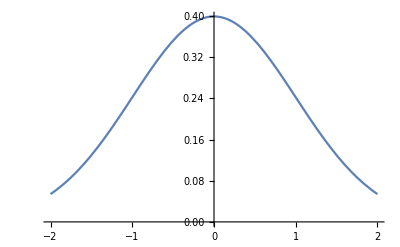

```mathematica
func=PDF[NormalDistribution[]];
Plot[func[x],{x,-2,2}]
```